## Useful functions

```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12,Magnification->1.6};
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

Get::noopen: Cannot open MaTeX`.

$Failed

C:\Users\conte\Desktop\Repository\31_resonances\code

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=z SphericalBesselY[l,z];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha[ra_,ka_,la_,ha_]:=RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]

beta[rb_,kb_,lb_,hb_]:=RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])
```

LEC=(Λ,a_(3-1)^(S-wave) [fm],C_(2-body) [MeV],C_(3-body) [MeV])
the triton-proton S-wave scattering length is used to calibrate the core parameter and
was obtained by R. Lazauskas.

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
a0a1NUCLmartinrimas=Import[NotebookDirectory[]<>"../data/a0-a1_nucl_Rimas-Martin.dat","Table"][[2;;]];
(* λ C0,D0 (Martin, 23) C0,D0 (Rimas, unprojected, 45) C0,Do (Rimas, projected, 67)*)
LECsNUCLmartinrimas=Import[NotebookDirectory[]<>"../data/LECs_nucl_Rimas-Martin.dat","Table"][[2;;]];

activeLEC=LECsNUCLmartinrimas[[All,{1,6,7}]];
a0a1REFERENCE=a0a1NUCLmartinrimas[[All,{8,9}]];
```

(non)local resonating-group potentials from a 2- and 3-body contact interaction for TRIMER-FERMION (ABC-A)

W_(non-local) takes the Energy (e_) in [MeV]

```mathematica
NormTF[core_?ArrayQ]:=1./Sqrt[Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] (Pi/(core[[i]][[2]]+core[[j]][[2]]))^1.5,{i,Length[core]},{j,Length[core]}]]]];

VlocTF[r_,lam_,Cc_,Dd_,Aa_,Bb_]:=Block[{eta2,eta3,w2,w3},
eta2=2. Cc/(2. (Aa+Bb)(3. Aa+3. Bb+2. lam))^(3./2.);
w2=3. (Aa+Bb) lam/(3. (Aa+Bb)+2. lam);
eta3=Dd/(6. (Aa+Bb)^2+16. (Aa+Bb) lam+2. lam^2)^(3./2.);
w3=(3. (Aa+Bb) lam ((Aa+Bb)+2. lam)/(3. (Aa+Bb)^2+8. (Aa+Bb) lam+lam^2));
eta2 Exp[-w2 r^2]+eta3  Exp[-w3 r^2]
];

WnolocTF[r_,rp_,Ee_,lam_,Cc_,Dd_,Aa_,Bb_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=(27./64.)(2 (Aa+Bb))^(-3./2.) (1./TwoMyOverHBsq);
a1=(Aa+9. Bb) 3./32.;
b1=(Aa+Bb) 9./16.;
c1=(9. Aa+Bb) 3./32.;

zeta2=-27./32. Cc/(2. (Aa+Bb)+lam)^(3./2.);
zeta3=-27./64. Dd/(2  (Aa+Bb)+5 lam)^(3./2.);

a2=3. (Aa^2+9. Bb^2+10. Aa Bb+(14. Aa+18. Bb) lam)/(16. (2. (Aa+Bb)+lam));
b2=18. (Aa+Bb) ((Aa+Bb)+2. lam)/(16. (2. (Aa+Bb)+lam));
c2=3. (9. Aa^2+Bb^2+10. Aa Bb+(6. Aa+2. Bb) lam)/(16. (2. (Aa+Bb)+lam));

a3=3. (Aa^2+9. Bb^2+10. Aa Bb+(16. Aa+36. Bb) lam+27. lam^2)/(16. (2. (Aa+Bb)+5. lam));
b3=18. ((Aa+Bb)^2+4. (Aa+Bb) lam+3. lam^2)/(16. (2. (Aa+Bb)+5. lam));
c3=3. (9. Aa^2+Bb^2+10. Aa Bb+(24. Aa+4. Bb) lam+3. lam^2)/(16. (2 (Aa+Bb)+5. lam));

-(4 Pi r rp) (
zeta1 Exp[-a1 (r^2+rp^2)] ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)+(Ll+1) Ll/r^2-TwoMyOverHBsq Ee) I^Ll  SphericalBesselJ[Ll,I b1 r rp]
-4 a1 b1 r rp Sum[(1-Ll^2+l^2) I^(l+1)/Sqrt[3] (2/Sqrt[5])^((Ll+l)/2) SphericalBesselJ[1+l,I b1 r rp],{l,-Ll,Ll}])
+I^Ll zeta2 SphericalBesselJ[Ll,I b2 r rp] Exp[-a2 r^2-c2 rp^2]
+I^Ll zeta3 SphericalBesselJ[Ll,I b3 r rp] Exp[-a3 r^2-c3 rp^2]
)
];
```

The function <SolveSecular> expects the variable <<momentum>> in  [fm^-1]
As  W_(non-local) takes the Energy (e_) in [MeV];
The core wave function is parametrized via the "a0={{c_1,α_1},{c_2,α_2},...,{c_N,α_N}}" array:
ϕ_core=(∑^N)_(i=1)c_i·e_^(-α_i/2∏_j (r^-)_j^2)

```mathematica
SolveSecular[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Amat=ConstantArray[0,{Npoints,Npoints}];

normsqu=NormTF[a00]^2;

Do[
If[a00[[ii]][[1]] a00[[jj]][[1]]≠0,

cij=a00[[ii]][[1]] a00[[jj]][[1]] normsqu;


amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]]],{i,1,Npoints}]];
wmat=Table[-hDif^3 TwoMyOverHBsq WnolocTF[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}]; 

Amat+=(cij (amat+wmat));

]
,{ii,1,Length[a00]},{jj,1,Length[a00]}];

Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat+=(Kmat+Dmat);

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);

tanDelta
]
```

```mathematica
SolveSecularF[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,c01_?NumberQ,a01_?NumberQ,c02_?NumberQ,a02_?NumberQ,TwoMyOverHBsq_?NumberQ]:=Block[{a00,hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Amat=ConstantArray[0,{Npoints,Npoints}];

a00={{c01,a01},{c02,a02}};

normsqu=NormTF[a00]^2;

Do[
If[a00[[ii]][[1]] a00[[jj]][[1]]≠0,

cij=a00[[ii]][[1]] a00[[jj]][[1]] normsqu;


amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]]],{i,1,Npoints}]];
wmat=Table[-hDif^3 TwoMyOverHBsq WnolocTF[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}]; 

Amat+=(cij (amat+wmat));

]
,{ii,1,Length[a00]},{jj,1,Length[a00]}];

Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat+=(Kmat+Dmat);

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);

tanDelta
]
```

numerical and physical parameters

```mathematica
nGrid=200;

nf={6,4}; (* number form for printing, only *)
k0FM=0.1;  (*initial momentum*)

rr=25.0;   (*Integration radius*)
αL=Get[LocalObject["3-1_CorePara_SwaveRimas"]]; (*what was the old αL for rimas*)

hbar=197.327053;
Mm=938.92;
m1=3 Mm;m2=Mm;
μ=m1 m2/(m1+m2);mh2=(2 μ)/(hbar)^2;
Print["E_0 = ",(k0FM hbar)^2/(2 μ)," MeV"]
λRange=Range[1,Length[activeLEC]];
```

LocalObject::nso: LocalObject[file:///C:/Users/conte/AppData/Roaming/Wolfram/Objects/3-1_CorePara_SwaveRimas] not found.

E_0 = 0.276473 MeV

```mathematica
findLogDivisions[{xmin_,xmax_},n_Integer]:=10^FindDivisions[Log10@{xmin,xmax},n]

GetERE[x_]:=Module[{localcore=x},

core=localcore;

tanDsL={};tanDpL={};
tanDs={};tanDp={};

Do[
momFM=Sqrt[2 μ energ]/hbar;
TanDelSwave=Chop[SolveSecular[rr,nGrid,momFM,0,λ,C0,D0,core,mh2]];
TanDelPwave=Chop[SolveSecular[rr,nGrid,momFM,1,λ,C0,D0,core,mh2]];
AppendTo[tanDs,{energ,TanDelSwave}];
AppendTo[tanDp,{energ,TanDelPwave}];
,{energ,ErangeMeV}];

tanDs=Reverse[Sort[tanDs,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)
tanDp=Reverse[Sort[tanDp,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)
(*AppendTo[tanDsL,tnDs];
AppendTo[tanDpL,tnDp];*)
(*Extract the ERE Parameters*)
Lrel = 0;
dataS=Transpose[{(Sqrt[2 μ ErangeMeV]/hbar),(Sqrt[2 μ ErangeMeV]/hbar)/tanDs⟦All,2⟧}];
EreS=Fit[dataS⟦f1;;f2⟧,{1,p^2},p];
a0tf=-Coefficient[EreS,p,0]^-1;
r0tf= Coefficient[EreS,p,2]*2.;
Lrel = 1;
dataP=Transpose[{(Sqrt[2 μ ErangeMeV]/hbar),(Sqrt[2 μ ErangeMeV]/hbar)^3/tanDp⟦All,2⟧}];
EreP=Fit[dataP⟦f1;;f2⟧,{1,p^2},p];
a1tf=-Coefficient[EreP,p,0]^-1;
r1tf= Coefficient[EreP,p,2]*2.;

{a0tf,r0tf,a1tf,r1tf}
]
```

```mathematica
PlotERE:=Module[{},(*Plot the Phaseshifts for each α and C that I used*)
phaseS=Table[Transpose[{tanDs⟦i,1⟧, ArcTan[tanDs⟦i,2⟧]}],{i,1,Length[tanDs⟦All,1⟧]}];
phaseP=Table[Transpose[{tanDp⟦i,1⟧, ArcTan[tanDp⟦i,2⟧]}],{i,1,Length[tanDp⟦All,1⟧]}];
(*---------*)
Tfits=(Fit[dataS⟦1;;Min[10,Length[dataS]]⟧,{1,p^2,p^4},p]); (*fit ere again*)
dataTS=dataS;dataTS⟦All,2⟧=dataTS⟦All,2⟧^-1 ;
Polesp=(p/.NSolve[Tfits-ⅈ p==0,{p}]) ; (*find pole positions*) PolesE=hbar^2 Polesp^2 / (2 μ);
Print["S Pole Poitions in momentum: ", Polesp];
Print["S Pole Poitions in energy:   ", PolesE];
(*---------*)
Tfitp=(Fit[dataP⟦1;;Min[10,Length[dataP]]⟧,{1,p^2,p^4},p]); (*fit ere again*)
dataTP=dataP;dataTP⟦All,2⟧=dataTP⟦All,2⟧^-1 ;
Polepp=(p/.NSolve[Tfitp-ⅈ p^3==0,{p}]) ; (*find pole positions*) PolepE=hbar^2 Polepp^2 / (2 μ);
Print["P Pole Poitions in momentum: ", Polepp];
Print["P Pole Poitions in energy:   ", PolepE];


GraphicsGrid[{{
Show[{ Plot[-(1/a0tf)+(1/2)r0tf k^2,{k,0,dataS⟦-1,1⟧}],ListPlot[dataS,PlotRange->{{dataS⟦1,1⟧,dataS⟦1,-1⟧},All}]},ImageSize->500,AxesLabel->{"E [MeV]","K CotTan[δ_(S - wave)] [fm^-1]"},PlotStyle->"Red", PlotLabel->" S-wave KCotδ compared with -1/a0+1/2r0 k^2"]
,
Show[{ Plot[-(1/a1tf)+(1/2)r1tf k^2,{k,0,dataP⟦-1,1⟧}],ListPlot[dataP,PlotRange->{{dataP⟦1,1⟧,dataP⟦1,-1⟧},All}]},ImageSize->500,AxesLabel->{"E [MeV]","K^3 CotTan[δ_(S - wave)] [fm^-3]"},PlotStyle->"Red",PlotLabel->" P-wave K^3Cotδ compared with -1/a0+1/2r0 k^2"]

},
{
Show[ListPlot[dataTS],Plot[Tfits^-1,{p,0,0.4},PlotRange->{Automatic,Automatic}],ImageSize->500,PlotLabel->"T matrix compared with the ERE^-1(O(k^4)) expansion"],
Show[ListPlot[dataTP],Plot[Tfitp^-1,{p,0,0.4},PlotRange->{Automatic,Automatic}],ImageSize->500,PlotLabel->"T matrix compared with the ERE^-1(O(k^4)) expansion"]

}
},ImageSize->1000]]
```

## Import density and fit wavefunctions

```mathematica
Martinϕ1=Cases[Import["..\data/abc_u_1.0_binf_r1b.dnst","Table"],{_?NumberQ,___}];
Mϕ1=Transpose[{Martinϕ1⟦All,1⟧,Sqrt[Martinϕ1⟦All,3⟧]}];
Martinϕ2=Cases[Import["..\data/abc_u_2.0_binf_r1b.dnst","Table"],{_?NumberQ,___}];
Mϕ2=Transpose[{Martinϕ2⟦All,1⟧,Sqrt[Martinϕ2⟦All,3⟧]}];
Martinϕ3=Cases[Import["..\data/abc_u_3.0_binf_r1b.dnst","Table"],{_?NumberQ,___}];
Mϕ3=Transpose[{Martinϕ3⟦All,1⟧,Sqrt[Martinϕ3⟦All,3⟧]}];
Martinϕ4=Cases[Import["..\data/abc_u_4.0_binf_r1b.dnst","Table"],{_?NumberQ,___}];
Mϕ4=Transpose[{Martinϕ4⟦All,1⟧,Sqrt[Martinϕ4⟦All,3⟧]}];
Martinϕ6=Cases[Import["..\data/abc_u_6.0_binf_r1b.dnst","Table"],{_?NumberQ,___}];
Mϕ6=Transpose[{Martinϕ6⟦All,1⟧,Sqrt[Martinϕ6⟦All,3⟧]}];
Martinϕ8=Cases[Import["..\data/abc_u_8.0_binf_r1b.dnst","Table"],{_?NumberQ,___}];
Mϕ8=Transpose[{Martinϕ8⟦All,1⟧,Sqrt[Martinϕ8⟦All,3⟧]}];
Martinϕ10=Cases[Import["..\data/abc_u_10.0_binf_r1b.dnst","Table"],{_?NumberQ,___}];
Mϕ10=Transpose[{Martinϕ10⟦All,1⟧,Sqrt[Martinϕ10⟦All,3⟧]}];
```

```mathematica
nk=3;
core={}; Do[core=AppendTo[core,ToExpression@Map[StringJoin[#,ToString[k]]&,{"C","Α"}]],{k,1,nk}];
wf=Total[Flatten[Table[core⟦i⟧⟦1⟧ⅇ^(-core⟦i⟧⟦2⟧ r^2) ,{i,Length[core]}]]];
(* Preliminary easy fit for starting point*)
core4=core/.FindFit[Mϕ4,wf,Flatten[core],r];
corefit=Transpose[{Flatten[core],Flatten[core4]}];




core1=core/.FindFit[Mϕ1,wf,corefit,r]; 
wf1    =Total[Flatten[Table[core1⟦i⟧⟦1⟧ⅇ^(-core1⟦i⟧⟦2⟧ r^2) ,{i,Length[core1]}]]];
core2=core/.FindFit[Mϕ2,wf,corefit,r]; 
wf2    =Total[Flatten[Table[core2⟦i⟧⟦1⟧ⅇ^(-core2⟦i⟧⟦2⟧ r^2) ,{i,Length[core2]}]]];
core3=core/.FindFit[Mϕ3,wf,corefit,r]; 
wf3    =Total[Flatten[Table[core3⟦i⟧⟦1⟧ⅇ^(-core3⟦i⟧⟦2⟧ r^2) ,{i,Length[core3]}]]];
core4=core/.FindFit[Mϕ4,wf,corefit,r];
wf4    =Total[Flatten[Table[core4⟦i⟧⟦1⟧ⅇ^(-core4⟦i⟧⟦2⟧ r^2) ,{i,Length[core4]}]]];
core6=core/.FindFit[Mϕ6,wf,corefit,r];
wf6    =Total[Flatten[Table[core6⟦i⟧⟦1⟧ⅇ^(-core6⟦i⟧⟦2⟧ r^2) ,{i,Length[core6]}]]];
core8=core/.FindFit[Mϕ8,wf,corefit,r]; 
wf8    =Total[Flatten[Table[core8⟦i⟧⟦1⟧ⅇ^(-core8⟦i⟧⟦2⟧ r^2) ,{i,Length[core8]}]]];
core10=core/.FindFit[Mϕ10,wf,corefit,r]; 
wf10    =Total[Flatten[Table[core10⟦i⟧⟦1⟧ⅇ^(-core10⟦i⟧⟦2⟧ r^2) ,{i,Length[core10]}]]];
Print["wf1 = ", wf1]
Print["wf2 = ", wf2]
Print["wf3 = ", wf3]
Print["wf4 = ", wf4]
Print["wf6 = ", wf6]
Print["wf8 = ", wf8]
Print["wf10 = ", wf10]
```

wf1 = 0.106373 ⅇ^(-0.371415 r^2)-1.36285 ⅇ^(-0.102385 r^2)+1.40205 ⅇ^(-0.102385 r^2)

wf2 = 0.159045 ⅇ^(-0.662473 r^2)+1.58368 ⅇ^(-0.140094 r^2)-1.53 ⅇ^(-0.140094 r^2)

wf3 = 0.189254 ⅇ^(-0.873276 r^2)-1.35096 ⅇ^(-0.162914 r^2)+1.41418 ⅇ^(-0.162914 r^2)

wf4 = 0.208715 ⅇ^(-1.03031 r^2)-1.34759 ⅇ^(-0.178617 r^2)+1.41757 ⅇ^(-0.178617 r^2)

wf6 = 0.232307 ⅇ^(-1.24303 r^2)+1.24292 ⅇ^(-0.198532 r^2)-1.16434 ⅇ^(-0.198532 r^2)

wf8 = 0.24585 ⅇ^(-1.37572 r^2)+1.22839 ⅇ^(-0.210204 r^2)-1.14476 ⅇ^(-0.210204 r^2)

wf10 = 0.257821 ⅇ^(-1.49207 r^2)+1.21622 ⅇ^(-0.221642 r^2)-1.12811 ⅇ^(-0.221642 r^2)

```mathematica
GraphicsGrid[{{
Show[ListPlot[Mϕ1,PlotRange->All,PlotStyle->Gray],Plot[wf1,{r,-1,10},PlotStyle->{Orange,Thick}],ImageSize->500, AxesLabel->{"WaveFunction","r [fm]"},PlotLabel->"Λ = 1 fm^-1"],
Show[ListPlot[Mϕ2,PlotRange->All,PlotStyle->Gray],Plot[wf2,{r,-1,10},PlotStyle->{Orange,Thick}],ImageSize->500, AxesLabel->{"WaveFunction","r [fm]"},PlotLabel->"Λ = 2 fm^-1"]},
{
Show[ListPlot[Mϕ3,PlotRange->All,PlotStyle->Gray],Plot[wf3,{r,-1,10},PlotStyle->{Orange,Thick}],ImageSize->500, AxesLabel->{"WaveFunction","r [fm]"},PlotLabel->"Λ = 3 fm^-1"],
Show[ListPlot[Mϕ4,PlotRange->All,PlotStyle->Gray],Plot[wf4,{r,-1,10},PlotStyle->{Orange,Thick}],ImageSize->500, AxesLabel->{"WaveFunction","r [fm]"},PlotLabel->"Λ = 4 fm^-1" ]},
{
Show[ListPlot[Mϕ6,PlotRange->All,PlotStyle->Gray],Plot[wf6,{r,-1,10},PlotStyle->{Orange,Thick}],ImageSize->500, AxesLabel->{"WaveFunction","r [fm]"},PlotLabel->"Λ = 6 fm^-1"],
Show[ListPlot[Mϕ8,PlotRange->All,PlotStyle->Gray],Plot[wf8,{r,-1,10},PlotStyle->{Orange,Thick}],ImageSize->500, AxesLabel->{"WaveFunction","r [fm]"},PlotLabel->"Λ = 8 fm^-1" ]},
{
Show[ListPlot[Mϕ10,PlotRange->All,PlotStyle->Gray],Plot[wf10,{r,-1,10},PlotStyle->{Orange,Thick}],ImageSize->500, AxesLabel->{"WaveFunction","r [fm]"},PlotLabel->"Λ = 10 fm^-1"],
ListPlot[{Mϕ1,Mϕ2,Mϕ3,Mϕ4,Mϕ6,Mϕ8,Mϕ10},PlotRange->All,Joined->True,ImageSize->400,PlotRange->Full,PlotLegends->{"Λ = 1 fm^-1","Λ = 2 fm^-1","Λ = 3 fm^-1","Λ = 4 fm^-1","Λ = 6 fm^-1","Λ = 8 fm^-1","Λ = 10 fm^-1"}]}
},ImageSize->1000]
```

-Graphics-

## Testing The method with different parameters (λ=4 fm^-1)

## Fast (Rmax = 10, Ngrid=20)

```mathematica
λλ=4;
mycore=core4;
rr=10;nGrid=20;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=20;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

## Medium (Rmax = 10, Ngrid=100)

```mathematica
λλ=4;
mycore=core4;
rr=10;nGrid=100;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=20;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

```mathematica
λλ=4;
mycore=core4;
rr=10;nGrid=100;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=20;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

## Double grid (Rmax = 10, Ngrid=200)

```mathematica
λλ=4;
mycore=core4;
rr=10;nGrid=200;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=20;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

```mathematica
λλ=4;
mycore=core4;
rr=10;nGrid=100;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=20;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

## Long (Rmax = 15, Ngrid=200)

```mathematica
λλ=4;
mycore=core4;
rr=15;nGrid=200;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=20;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

```mathematica
λλ=4;
mycore=core4;
rr=10;nGrid=100;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=20;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

## Calculate all the cut-off

```mathematica
λλ=4;
mycore=core4;
rr=10;nGrid=20;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.01;
k0FMax=0.3;
Divisions=20;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*---------------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

## Fit the core from the ERE parameters

```mathematica
(* I need a simple function to contain the fit*)
FitEre[x_?(VectorQ[#, NumericQ]&)]:=Module[{Aa0=x[[1]],Cc1=x[[2]],Aa1=x[[3]]},
mycore={{1.,Aa0},{Cc1,Aa1}};
ERE=GetERE[mycore];
a0tf=ERE⟦1⟧;
r0tf=ERE⟦2⟧;
a1tf=ERE⟦3⟧;
iIi=iIi+1;
Print["iter: ", iIi, "       core={1, ",Aa0,", ",Cc1,", ", Aa1"}     |     ERE = ", ERE  , "     |    to goal: ", {a0tf^-1,r0tf,a1tf^-1}-Goal ];
{a0tf^-1,r0tf,a1tf^-1}-Goal
]
```

λ = Λ^2/4 = 4.0000  ⇒ Λ = 4.0000 ; C_0 = -505.1500 ; D_0 = 1426.7500

Core = {{-1.34759,0.178617},{0.208715,1.03031},{1.41757,0.178617}}

ERE =      a0 = 9.99847     r0 = 6.84093     a1 = 333.18     r1 = -0.344261

S Pole Poitions in momentum: {-0.158053+0.128757 ⅈ,0.+0.161528 ⅈ,0.-0.419043 ⅈ,0.158053+0.128757 ⅈ}

S Pole Poitions in energy:   {0.232299-1.12527 ⅈ,-0.721359+0. ⅈ,-4.85479+0. ⅈ,0.232299+1.12527 ⅈ}

P Pole Poitions in momentum: {-0.194228+0.162926 ⅈ,0.-0.0994097 ⅈ,0.+0.200429 ⅈ,0.194228+0.162926 ⅈ}

P Pole Poitions in energy:   {0.309088-1.7498 ⅈ,-0.273219+0. ⅈ,-1.11065+0. ⅈ,0.309088+1.7498 ⅈ}

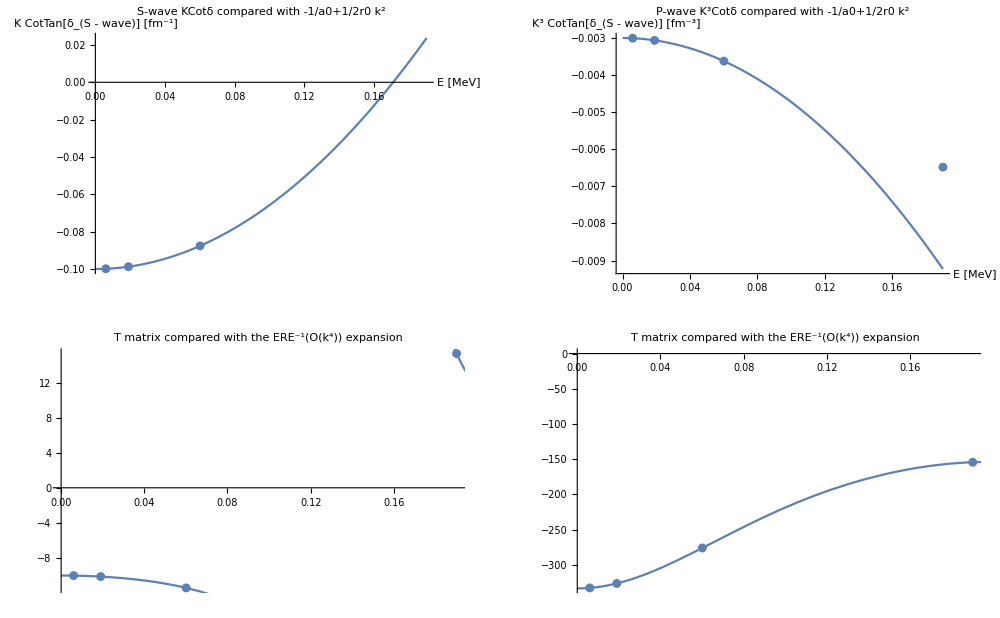

```mathematica
(*Go with the fit*)
λλ=4;
mycore=core4;
rr=10;nGrid=20;
f1=1;f2=3; 

k0FMin=0.01;
k0FMax=0.1;
Divisions=3;



(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;

(*--------- Test that all is ok------------*)
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==λλ&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
Print["λ = Λ^2/4 = ",NumberForm[λ,nf],"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]];
Print["Core = ",mycore]
ERE=GetERE[mycore];
Print["ERE = ","     a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧]
PlotERE
```

```mathematica
(*--------run fit---------*)
iIi=0;
xini={1.2,3.1,2.1};
Goal={3.32^-1, 2.55,-20.23^-1};
CoreFitted=FindRoot[FitEre[x],{x,xini},PrecisionGoal->4,AccuracyGoal->4]
```

iter: 1core={1, 1.2, 3.1, 2.1 }     |     ERE = {0.437701,-3.45891,0.0279198,3500.13}     |    to goal: {1.98346,-6.00891,35.8663}

iter: 2core={1, 1.2, 3.1, 2.1 }     |     ERE = {0.437701,-3.45891,0.0279198,3500.13}     |    to goal: {1.98346,-6.00891,35.8663}

iter: 3core={1, 1.2, 3.1, 2.1 }     |     ERE = {0.437701,-3.45891,0.0279198,3500.13}     |    to goal: {1.98346,-6.00891,35.8663}

iter: 4core={1, 1.2, 3.1, 2.1 }     |     ERE = {0.437701,-3.45891,0.0279198,3500.13}     |    to goal: {1.98346,-6.00891,35.8663}

iter: 5core={1, 1.2, 3.1, 2.1 }     |     ERE = {0.437701,-3.45891,0.0279198,3500.13}     |    to goal: {1.98346,-6.00891,35.8663}

iter: 6core={1, 1.74038, -17.1813, 3.00842 }     |     ERE = {0.0214003,65.9395,-0.000942982,-684503.}     |    to goal: {46.427,63.3895,-1060.42}

iter: 7core={1, 1.25404, 1.07187, 2.19084 }     |     ERE = {0.475695,-2.80187,0.0303173,3011.65}     |    to goal: {1.80098,-5.35187,33.0339}

iter: 8core={1, 1.25404, 1.07187, 2.19084 }     |     ERE = {0.475695,-2.80187,0.0303173,3011.65}     |    to goal: {1.80098,-5.35187,33.0339}

iter: 9core={1, 1.25404, 1.07187, 2.19084 }     |     ERE = {0.475695,-2.80187,0.0303173,3011.65}     |    to goal: {1.80098,-5.35187,33.0339}

iter: 10core={1, 1.25404, 1.07187, 2.19084 }     |     ERE = {0.475695,-2.80187,0.0303173,3011.65}     |    to goal: {1.80098,-5.35187,33.0339}

iter: 11core={1, 1.25404, 1.07187, 2.19084 }     |     ERE = {0.475695,-2.80187,0.0303173,3011.65}     |    to goal: {1.80098,-5.35187,33.0339}

iter: 12core={1, 0.274982, -7.11776, -0.566135 }     |     ERE = {9.99847,6.84093,333.181,-0.34426}     |    to goal: {-0.20119,4.29093,0.0524329}

$Aborted